```mathematica
Nest[(1+#)^2&,{1,2,3},3]
```

{676,10201,84100}

```mathematica
(1+(1+(1+1)^2)^2)^2
```

676

```mathematica
Nest[ # (1-#)&,0.2,2]

Logis[r_]:=Nest[r # (1-#)&,Range[0,1,0.1],1000];
Logis[3.3]

ListPlot[Table[Thread[{r,}],{r,0,4,0.01}]]
```

0.1344

{0.,0.479427,0.823603,0.823603,0.479427,0.479427,0.479427,0.823603,0.823603,0.479427,0.}

-Graphics-

```mathematica
Clear[Logistic,r];
Clear[x,nn];
(*定义逻辑斯蒂映射：*)
Logistic[r_,x_]:=r x(1-x);

(*需要放在Manipulate里的参数：x0 = 0.2;r=1;*)
nn=18;(*iterNum*)

(*定义用于绘制逻辑斯蒂函数曲线和对角线直线：*)
Baseplot[r_,plotXMin_,plotXMax_]:= Plot[ {Logistic[r,x], y=x },{x,plotXMin,plotXMax}];

(*迭代的蛛网直线的：*)
pts = NestList[Logistic[r,#]&,x,nn];

 (*蜘蛛网的点，很罗嗦：lines =ListLinePlot[{{0.3,0},{0.3,0.21},{0.21,0.21},{0.21,0.1659},{0.1659,0.1659},{0.1659,0.13837719}}];*)
l0=Table[pts[[i+j]],{i,1,nn,2},{j,0,1,1}];
l1=Table[pts[[i]],{i,2,nn,2},{j,2}];
l2=Table[pts[[i+j]],{i,2,nn,2},{j,0,1,1}];
l3=Table[pts[[i]],{i,3,nn,2},{j,2}];
lines = Flatten[Table[{l0[[i]],l1[[i]],l2[[i]],l3[[i]]},{i,1,nn/2-1,1}],1];
lines=Insert[lines,{pts[[1]],0},1];
SpiderLines[r_,x_]:=Evaluate[lines];
SpiderPlot[r_,x_]:=ListLinePlot[SpiderLines[r,x],PlotStyle->{Tiny,Red}];

(*输出绘制：*)
Manipulate[Show[Baseplot[r,-0.05,1.05],SpiderPlot[r,x0],AspectRatio->1],{r,0.1,6},{x0,0,1}]
```

Show::gcomb: 无法合并 Show[Baseplot[4.14,-0.05,1.05],SpiderPlot[4.14,0.316],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[0.87,-0.05,1.05],SpiderPlot[0.87,0.223],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[2.41,-0.05,1.05],SpiderPlot[2.41,0.297],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[1.54,-0.05,1.05],SpiderPlot[1.54,0],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[2.41,-0.05,1.05],SpiderPlot[2.41,0.297],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[1.54,-0.05,1.05],SpiderPlot[1.54,0],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[3.6,-0.05,1.05],SpiderPlot[3.6,0.323],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[1,-0.2,1.2],SpiderPlot[1,0.612],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[3.6,-0.05,1.05],SpiderPlot[3.6,0.323],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[1,-0.2,1.2],SpiderPlot[1,0.612],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[3.58],SpiderPlot[3.58,0.2],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[2.06],SpiderPlot[2.06,0.2],AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[2.06],,AspectRatio→1] 中的图形对象.

Show::gcomb: 无法合并 Show[Baseplot[2.06],SpiderPlot[2.06,0.2],AspectRatio→1] 中的图形对象.

```mathematica
l0=Table[pts[[i+j]],{i,1,10,2},{j,0,1,1}]
l1=Table[pts[[i]],{i,2,10,2},{j,2}]
l2=Table[pts[[i+j]],{i,2,10,2},{j,0,1,1}]
l3=Table[pts[[i]],{i,3,10,2},{j,2}]
lines = Flatten[Table[{l0[[i]],l1[[i]]},{i,1,5,1}],1]
```

{{0.3,0.21},{0.1659,0.138377},{0.119229,0.105013},{0.0939856,0.0851523},{0.0779014,0.0718328}}

{{0.21,0.21},{0.138377,0.138377},{0.105013,0.105013},{0.0851523,0.0851523},{0.0718328,0.0718328}}

{{0.21,0.1659},{0.138377,0.119229},{0.105013,0.0939856},{0.0851523,0.0779014},{0.0718328,0.0666728}}

{{0.1659,0.1659},{0.119229,0.119229},{0.0939856,0.0939856},{0.0779014,0.0779014}}

{{0.3,0.21},{0.21,0.21},{0.1659,0.138377},{0.138377,0.138377},{0.119229,0.105013},{0.105013,0.105013},{0.0939856,0.0851523},{0.0851523,0.0851523},{0.0779014,0.0718328},{0.0718328,0.0718328}}

1.2 (1-x) x

0.192

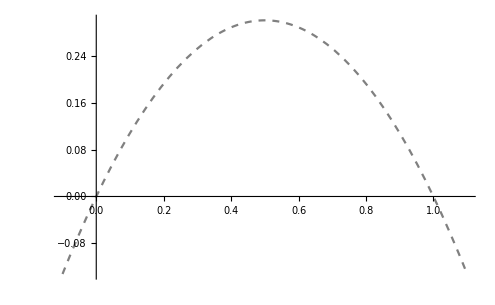

```mathematica
(*需要放在Manipulate里的参数：Logistic[r_,x_]:=r x(1-x);*)
Clear[res];
ls = Logistic[1.2,x]
res[x_] := Evaluate[ls];
res[0.2]
(*定义用于绘制逻辑斯蒂函数曲线和对角线直线：*)
Plot[ {res [x]},{x,-0.1,1.1},PlotStyle->{Gray,Dashed,Tiny}]
```

```mathematica
fd =NestList[ Logistic[r,#]&,x,4]
fda[r_,x_]:=Evaluate[fd];
l0=Table[pts[[i+j]],{i,1,4,2},{j,0,1,1}]
fdp[r_,x_]:=Evaluate[l0];
fda[3.3,0.824]
fdp[1,0.3]
```

{x,r (1-x) x,r^2 (1-x) x (1-r (1-x) x),r^3 (1-x) x (1-r (1-x) x) (1-r^2 (1-x) x (1-r (1-x) x)),r^4 (1-x) x (1-r (1-x) x) (1-r^2 (1-x) x (1-r (1-x) x)) (1-r^3 (1-x) x (1-r (1-x) x) (1-r^2 (1-x) x (1-r (1-x) x)))}

{{x,r (1-x) x},{r^2 (1-x) x (1-r (1-x) x),r^3 (1-x) x (1-r (1-x) x) (1-r^2 (1-x) x (1-r (1-x) x))}}

{0.824,0.478579,0.823486,0.479678,0.823637}

{{0.3,0.21},{0.1659,0.138377}}

```mathematica
x-  (Logistic[r,x] / D[Logistic[r,x],x]) //FullSimplify
```

x^2/(-1+2 x)

```mathematica
newt[x_]:=x^2/(-1+2 x);
newt[0.21]
```

-0.0760345

```mathematica
SpiderPlot
zhizhuplot[3.5,0.99999,36]
```

zhizhuplot[3.5,0.99999,36]

```mathematica
ClearAll[pts]
Logistic[r_,x_]:=r x (1-x);nn=18;Baseplot[r_,plotXMin_,plotXMax_]:=Plot[{Logistic[r,x],x},{x,plotXMin,plotXMax}];pts[r_,x_]:=NestList[Logistic[r,#]&,x,nn];
Manipulate[Show[Baseplot[r,-0.05,1.05],Graphics[Line@Prepend[Flatten[BlockMap[{{#[[1]],#[[2]]},{#[[2]],#[[2]]}}&,pts[r,x0],2,1],1],{x0,0}]],AspectRatio->1],{r,0.1,6},{x0,0,1}]
```

Show::gcomb: 无法合并 Show[Baseplot[3.635,-0.05,1.05],,AspectRatio→1] 中的图形对象.

```mathematica
ClearAll[pts]
Logistic[r_,x_]:=r x (1-x);nn=30;Baseplot[r_,plotXMin_,plotXMax_]:=Plot[{Logistic[r,x],x},{x,plotXMin,plotXMax}];pts[r_,x_]:=NestList[Logistic[r,#]&,x,nn];
Manipulate[Show[Baseplot[r,-0.05,1.05],Graphics[Line@Prepend[Flatten[BlockMap[{{#[[1]],#[[2]]},{#[[2]],#[[2]]}}&,pts[r,x0],2,1],1],{x0,0}]],AspectRatio->1],{r,0.1,4},{x0,0,1}]
```

```mathematica
NestList[Logistic[2,#]&,0.3,5]
Range[10]
BlockMap[f,Range[10],2,1]
BlockMap[{{#[[1]],#[[2]]},{#[[2]],#[[2]]}}&,Range[10],2,1]
(*lines =ListLinePlot[{{0.3,0},{0.3,0.21},{0.21,0.21},{0.21,0.1659},{0.1659,0.1659},{0.1659,0.13837719}}];*)
```

{0.3,0.42,0.4872,0.499672,0.5,0.5}

{1,2,3,4,5,6,7,8,9,10}

{f[{1,2}],f[{2,3}],f[{3,4}],f[{4,5}],f[{5,6}],f[{6,7}],f[{7,8}],f[{8,9}],f[{9,10}]}

{{{1,2},{2,2}},{{2,3},{3,3}},{{3,4},{4,4}},{{4,5},{5,5}},{{5,6},{6,6}},{{6,7},{7,7}},{{7,8},{8,8}},{{8,9},{9,9}},{{9,10},{10,10}}}

```mathematica
(*{#[[1]],#[[2]]}&,{1,2,3,4,5,6,7,8,9,10}*)
tfunc[ls_]:={ls[[1]],ls[[2]]};
tfunc[{1,2,3,4,5,6,7,8,9,10}]
```

{1,2}

```mathematica
Manipulate[Plot[{a x (1-x),x},{x,0,1},Epilog->Line[{#[[All,{1,1}]],#}ᵀ~Flatten~1&@Partition[NestList[a # (1-#)&,x0,40],2,1]],AspectRatio->Automatic],{a,1,4},{{x0,0.6},0,1}]
```

```mathematica
Manipulate[Plot[{a x (1-x),x},{x,0,1},Epilog->Line[{#[[All,{1,1}]],#}ᵀ~Flatten~1&@Partition[NestList[a # (1-#)&,x0,40],2,1]],AspectRatio->Automatic],{a,1,4},{{x0,0.6},0,1}]

作者：无影东瓜
链接：https://www.zhihu.com/question/55683496/answer/148176925
来源：知乎
著作权归作者所有。商业转载请联系作者获得授权，非商业转载请注明出处。
```